```mathematica
"Eskilson
```

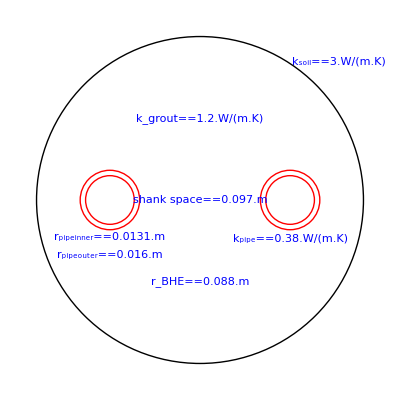

```mathematica
rhof=988.04 (*fluid density[kg/m^3]*); Qi= 0.000266 (*flow-rate[m^3/s]*); rpi=0.0131 (*inner radius[m]*); mu=0.0005465 (*dynamic viscosity [Pa.s]*); cpf=4182 (*fluid specificheat capacity [J/kgK]*); kfluid=0.64 (*fluid thermal conductivity [W/(m.K)]*); kpipe=0.38 (*pipe thermal conductivity [W/(m.K)]*); rpo=0.016 (*outer radius of pipe [m]*); kgrout=1.2 (*grout thermal conductivity [W/(m.K)]*); ss=0.097 (*shank space [m]*); rb=0.088(*borehole radius [m]*); ks=3 (*ground thermal conductivity [W/(m.K)]*);Hb=50 (*Borehole depth [m]*);
Graphics[{Circle[{0,0},rb],{Red,Circle[{-ss/2,0},rpo],Circle[{ss/2,0},rpo],Circle[{ss/2,0},rpi],Circle[{-ss/2,0},rpi]},{Blue,Inset[Subscript[k, grout]==kgrout .(W/(m.K)),{0,rb/2}],Inset[Subscript[k, soil]==ks .(W/(m.K)),{rb*0.85,rb*0.85}],Inset[Subscript[k, pipe]==kpipe .(W/(m.K)),{ss/2,-rpo*1.3}],Inset[Subscript[r, pipeinner]==rpi .(m),{-ss/2,-rpi*1.5}],Inset[Subscript[r, pipeouter]==rpo .(m),{-ss/2,-rpi*1.5-0.01}],Inset[shank space==ss .(m),{0,0}],Inset[Subscript[r, BHE]==rb .(m),{0,-rb/2}]}}]
```

```mathematica
Vfluid=Qi/(π*rpi^2);
Re1=(rhof*Vfluid*2*rpi)/mu;
Pr=(cpf*mu)/kfluid;
ff=(0.79*Log[Re1]-1.64)^-2;
NUpi=((ff/8)*(Re1-1000)*Pr)/(1+12.7*(ff/8)^(1/2)*(Pr^(2/3)-1));
Radv=1/(NUpi*kfluid*π) ;
Rconva=1/(2*π*kpipe)*Log[rpo/rpi];
x1U=Log[(√(4*rb^2*2*rpo^2))/(2*rpo)]/Log[(2*rb)/(2 √2*rpo)];
Rg=ArcCosh[(4*rb^2+4*rpo^2-ss^2)/(8*rb*rpo)]/(2*π*kgrout)*(1.601-0.888*ss/(2*rb));
Rconvb=x1U*Rg;
Rfig=Radv+Rconva+Rconvb;
Rgs=(1-x1U)*Rg;
Rar=ArcCosh[(2*ss^2-4*rpo^2)/(4*rpo^2)]/(2*π*kgrout);
Rgg=(2*Rgs*(Rar-2*x1U*Rg))/(2*Rgs-Rar+2*x1U*Rg);
u1=1/Rfig+1/Rgs+1/Rgg;
R1D=Rfig+Rgs;
R12D=1/Rgg((u1*Rfig*Rgg)^2-Rfig^2);
β1=1/(rhof*cpf*Qi*R1D);
β2=1/(rhof*cpf*Qi*R1D); 
β12=1/(rhof*cpf*Qi*R12D);
β0=(β2-β1)/2;
γ1=√((β1+β2)^2/4+β12*(β1+β2));
δ1=1/γ1*(β12+(β1+β2)/2);
```

```mathematica
R1D
```

0.282255

```mathematica
R12D
```

-4.48759

```mathematica
f1[z1_]:=ⅇ^(β0*z1)*(Cosh[γ1*z1]-δ1*Sinh[γ1*z1]); 
f2[z1_]:=ⅇ^(β0*z1)*β12/γ1*Sinh[γ1*z1];
f3[z1_]:=ⅇ^(β0*z1)*(Cosh[γ1*z1]+δ1*Sinh[γ1*z1]);
f4[z1_]:=ⅇ^(β0*z1)*(β1*Cosh[γ1*z1]-(δ1*β1+β2*β12/(γ1))*Sinh[γ1*z1]);
f5[z1_]:=ⅇ^(β0*z1)*(β2*Cosh[γ1*z1]+(δ1*β2+β1*β12/(γ1))*Sinh[γ1*z1]);
```

```mathematica
(*Tfout=(f1[Hb]+f2[Hb])/(f3[Hb]-f2[Hb])*Tfin+∫_0^Hb (Tb[x]*f4[Hb-x]+f5[Hb-x])/(f3[Hb]-f2[Hb])ⅆx* )
```

```mathematica
Δx[n_]:=Hb/n;
fI[x_]:=(Tb[x]*f4[Hb-x]+f5[Hb-x])/(f3[Hb]-f2[Hb]) ;
Tb[x_]:=15*x/x;
I1[n_]:=Δx[n]/2*(fI[0.01]+fI[Hb]+2*(∑_(x=1)^(n-1) fI[0+x*Δx[n]]));
Tfin:=40;
Tfout[n_]:=(f1[Hb]+f2[Hb])/(f3[Hb]-f2[Hb])*Tfin+I1[n]
```

```mathematica
Tfout[100]
```

41.7509